```mathematica
(* Created with Mathematica 8.0.1 *)
(* Code version 1.3 // w(a)CDM *)
```

```mathematica
Quit[]
```

```mathematica
(* Definitions *)
```

```mathematica
(* Set the directory *)
```

```mathematica
SetDirectory[NotebookDirectory[]];
Needs["ErrorBarPlots`"];
Needs["PlotLegends`"];
Off[General::"obspkg",NIntegrate::"inumr",NIntegrate::ncvb];
deaddrop="C:\\Users\\savvas\\Dropbox\\Work\\leavas";
```

```mathematica
(* Various scales and data *)
```

```mathematica
(* Maximum Likelihood value for Ωb*h^2 from WMAP7 *)
Ωbh2=2.258/100;
h=0.704;
ob0=Ωbh2/h^2;
```

```mathematica
(* DE equation of state w(a) and energy density f(a) *)
w[a_,w0_,wa_]:=w0+wa(1-a)
f[a_,w0_,wa_]:=a^(-3 (1+w0+wa)) ⅇ^(3 (-1+a) wa)
(*
 Tests: 
-1-1/3 a D[Log[f[a,w0,wa]],a]-w[a,w0,wa]//Simplify
Exp[-3Integrate[(1+w[aa,w0,wa])/aa,{aa,1,a},GenerateConditions->False]]//PowerExpand//FullSimplify
 *)
```

```mathematica
(* Subscript[Ω, r]=Subscript[Ω, γ]+Subscript[Ω, ν] see PDG *) 
Ωγ=2.469 10^-5 h^-2;Neff=3.04;Ωr=Ωγ(1+0.2271 Neff);
(* E=H/H0 for the CPL model *) 
H[a_?NumberQ,om_?NumberQ,ok_?NumberQ,w0_?NumberQ,wa_?NumberQ]:=Sqrt[a^-3 om+a^-2 ok+a^-4 Ωr+(1-om-ok-Ωr)f[a,w0,wa]]
(* Sound speed *) cs[a_?NumberQ,ob_?NumberQ]:=1/√(3(1+((3ob)/(4Ωγ))a));
```

```mathematica
fk[x_?NumberQ,ok_?NumberQ]:=Sin[√Abs[ok] x]/(√Abs[ok])/;ok<0
fk[x_?NumberQ,ok_?NumberQ]:=x/;ok==0
fk[x_?NumberQ,ok_?NumberQ]:=Sinh[√Abs[ok] x]/(√Abs[ok])/;ok>0
(* Alternatively 1/(√-ok)Sin[√-ok x] would work just as well *)
```

```mathematica
(* Redshift at decoupling (see Eqs. (66)-(68) in Komatsu et al.2009) *)
zcmb[om_?NumberQ,ob_?NumberQ]:=1048(1+0.00124(ob h^2)^-0.738)(1+((0.0783(ob h^2)^-0.238)/(1+39.5(ob h^2)^0.763))(om h^2)^(0.560/(1+21.1(ob h^2)^1.81)))
(* Drag redshift (see Eq. (4) of Hu astro-ph/9709112) *)
zdrag[om_?NumberQ,ob_?NumberQ]:=1291 ((om h^2)^0.251)/(1+0.659 (om h^2)^0.828)(1+(0.313(om h^2)^-0.419(1+0.607(om h^2)^0.674))(ob h^2)^(0.238(om h^2)^0.223))
(* Proper (not comoving) angular diameter distance with curvature, see Komatsu et al. 0803.0547  *)
DA[z_?NumberQ,om_?NumberQ,ok_?NumberQ,w0_?NumberQ,wa_?NumberQ]:=1/(1+z)fk[NIntegrate[1/H[1/(1+z1),om,ok,w0,wa],{z1,0,z}],ok]
(* Comoving sound horizon at drag redshift (see Percival et al: 0907.1660 Section 6 *)
rs[ze_,om_?NumberQ,ok_?NumberQ,ob_?NumberQ,w0_?NumberQ,wa_?NumberQ]:=NIntegrate[cs[x,ob]/(x^2H[x,om,ok,w0,wa]),{x,0,1/(1+ze[om,ob])}]
(* Dilation scale *)
Dv[zbao_,om_?NumberQ,ok_?NumberQ,w0_?NumberQ,wa_?NumberQ]:=((DA[zbao,om,ok,w0,wa](1+zbao))^2 zbao/H[1/(1+zbao),om,ok,w0,wa])^(1/3)
(* Scaled distance at recombination *)
R[om_,ok_,ob_,w0_,wa_]:=√om DA[zcmb[om,ob],om,ok,w0,wa](1+zcmb[om,ob])
(* Angular scale of sound horizon at recombination *)
la[om_,ok_,ob_,w0_,wa_]:=π (DA[zcmb[om,ob],om,ok,w0,wa](1+zcmb[om,ob]))/rs[zcmb,om,ok,ob,w0,wa]
(* Distance for SnIa calculation *)
 rr[xx_,om_,ok_,w0_,wa_]:=DA[xx,om,ok,w0,wa](1+xx)
```

```mathematica
(* CMB and BAO χ^2 terms *)
```

```mathematica
(* CMB: WMAP9 *)
```

```mathematica
(* Central values and 1-σ errors for {Subscript[l, a], R, zcmb} from WMAP9 *)
(* See 1212.5226, page 21 for details *)
datacmb={302.40,1.7246,1090.88};
(* Inverse Covariance Matrix using  for {Subscript[l, a], R, zcmb} *)
invcov=({{3.182, 18.253, -1.429}, {18.253, 11887.879, -193.808}, {-1.429, -193.808, 4.556}});
(* χ^2 for R *)
vec[om_,ok_,ob_,w0_,wa_]:={la[om,ok,ob,w0,wa]-datacmb[[1]],R[om,ok,ob,w0,wa]-datacmb[[2]],zcmb[om,ob]-datacmb[[3]]};
chi2R[om_,ok_,w0_,wa_]:=vec[om,ok,ob0,w0,wa].invcov.vec[om,ok,ob0,w0,wa]
```

```mathematica
(* BAO: SDSS 7 + WiggleZ + 6dFGS *)
```

```mathematica
(* BAO data, see 1205.0364 *)
databao={{0.106,0.336,0.015},{0.2,0.1905,0.0061},{0.35,0.1097,0.0036},{0.44,0.0916,0.0071},{0.6,0.0726,0.0034},{0.73,0.0592,0.0032}};
Cijinv=({{4444, 0, 0, 0, 0, 0}, {0, 30318, -17312, 0, 0, 0}, {0, -17312, 87046, 0, 0, 0}, {0, 0, 0, 23857, -22747, 10586}, {0, 0, 0, -22747, 128729, -59907}, {0, 0, 0, 10586, -59907, 125536}});
lBAO[om_,ob_,h_]:=1/(2997.9/h)44.5Log[9.83/(om h^2)]/(√(1+10(ob h^2)^(3/4)));
dz[zbao_,om_,ok_,w0_,wa_]:=lBAO[om,ob0,h]/Dv[zbao,om,ok,w0,wa]
vecbao[om_,ok_,ob_,w0_,wa_]:=Table[(databao[[i,2]]-dz[databao[[i,1]],om,ok,w0,wa]),{i,1,Length[databao]}];
chi2bao[om_,ok_,w0_,wa_]:=vecbao[om,ok,ob0,w0,wa].Cijinv.vecbao[om,ok,ob0,w0,wa]
```

```mathematica
(* SnIa χ^2 term *)
```

```mathematica
(* Read the SnIa data *)
```

```mathematica
Off[NIntegrate::"inumr"];Off[NIntegrate::"nlim"];
datasets={Constitution,Union2,Union21};
descript={{Word,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number},{Word,Number,Number,Number,Number,Number,Number,Number,Number,Number},{Word,Number,Number,Number,Number}};
sigmaint={0,0,0};
location={{2,10,11},{2,3,4},{2,3,4}};
Do[datanw[ds]=ReadList[".\\data\\"<>ToString[datasets[[ds]]]<>".txt",descript[[ds]]];,{ds,1,Length[datasets]}];
set=3;
ndat=Length[datanw[set]];
data=datanw[set][[All,location[[set]]]];
sint=sigmaint[[set]];
```

```mathematica
(* chi^2 // minimize over h *)
```

```mathematica
chi2fa[om_,ok_,w0_,wa_]:=Sum[(data[[i,2]]-5 Log[10,rr[data[[i,1]],om,ok,w0,wa]*(1+data[[i,1]])])^2/(data[[i,3]]^2+sint^2),{i,1,ndat}];
chi2fb[om_,ok_,w0_,wa_]:=Sum[(data[[i,2]]-5 Log[10,rr[data[[i,1]],om,ok,w0,wa]*(1+data[[i,1]])])/(data[[i,3]]^2+sint^2),{i,1,ndat}];
chi2fc=Sum[1/(data[[i,3]]^2+sint^2),{i,1,ndat}];
chi2SN[om_,ok_,w0_,wa_]:=chi2fa[om,ok,w0,wa]-chi2fb[om,ok,w0,wa]^2/chi2fc;
```

```mathematica
(* Growth rate χ^2 term *)
```

```mathematica
(* The growth rate data *)
```

```mathematica
datagrowth={{0.02,0.36,0.04},{0.067,0.423,0.055},{0.17,0.51,0.06},{0.35,0.44,0.05},{0.77,0.49,0.18},{0.25,0.3512,0.0583},{0.37,0.4602,0.0378},{0.22,0.42,0.07},{0.41,0.45,0.04},{0.6,0.43,0.04},{0.78,0.38,0.04},{0.57,0.451,0.025},{0.3,0.407,0.055},{0.4,0.419,0.041},{0.5,0.427,0.043},{0.6,0.433,0.067}};
```

```mathematica
(* chi^2 part *)
```

```mathematica
(* Various models for γ(z) *)
γ[0][z_,g0_,g1_]:=g0
γ[1][z_,g0_,g1_]:=(g0+g1 z)/;z≤0.5
γ[1][z_,g0_,g1_]:=(g0+g1/2)/;z>0.5
γ[2][z_,g0_,g1_]:=(g0+g1 z/(1+z))
```

```mathematica
(* The growth rate and fσ8 (A in the paper) *)
fgrowth[z_?NumberQ,om_?NumberQ,ok_?NumberQ,w0_?NumberQ,wa_?NumberQ,γ0_?NumberQ,γ1_?NumberQ,gammamodel_]:=((om (1+z)^3)/H[1/(1+z),om,ok,w0,wa]^2)^γ[gammamodel][z,γ0,γ1]
fσ8z[z_?NumberQ,om_?NumberQ,ok_?NumberQ,w0_?NumberQ,wa_?NumberQ,γ0_?NumberQ,γ1_?NumberQ,σ8_?NumberQ,gammamodel_]:=σ8 Exp[NIntegrate[1/aa fgrowth[1/aa-1,om,ok,w0,wa,γ0,γ1,gammamodel],{aa,1,1/(1+z)}]] fgrowth[z,om,ok,w0,wa,γ0,γ1,gammamodel]
```

```mathematica
(* Same as above but for wCDM models *)
δ[a_,w_,Ω_]:=a Hypergeometric2F1[1/(-3w),1/2-1/(2 w),1-5/(6 w),a^(-3 w) (1-1/Ω)]
fwCDM[z_,w_,Ω_]:=aa D[Log[δ[aa,w,Ω]],aa]/.aa->1/(1+z)
fσ8wCDM[z_,w_,Ω_,σ8_]:=fwCDM[z,w,Ω]σ8  δ[1/(1+z),w,Ω]/δ[1,w,Ω]
```

```mathematica
(* The chi^2 *)
chi2growth[om_?NumberQ,ok_?NumberQ,w0_?NumberQ,wa_?NumberQ,γ0_?NumberQ,γ1_?NumberQ,σ8_?NumberQ,gammamodel_]:=Sum[(1/datagrowth[[i,3]](datagrowth[[i,2]]-fσ8z[datagrowth[[i,1]],om,ok,w0,wa,γ0,γ1,σ8,gammamodel]))^2,{i,1,Length[datagrowth]}]
```

```mathematica
(* end *)
```

```mathematica
(* Combine all data (SnIa, CMB, BAO, Growth) *)
```

```mathematica
chi2total[om_?NumberQ,ok_?NumberQ,w0_?NumberQ,wa_?NumberQ,γ0_?NumberQ,γ1_?NumberQ,σ8_?NumberQ,gammamodel_]:=chi2R[om,ok,w0,wa]+chi2bao[om,ok,w0,wa]+ chi2SN[om,ok,w0,wa]+chi2growth[om,ok,w0,wa,γ0,γ1,σ8,gammamodel]
```

```mathematica
(* Cache *)
```

```mathematica
σ80=0.8;
fmin1={730.4088829`10.315111039745918,{574.2271905777252,{om->0.27232389285506203,g0->0.5969730932189693}}};
fmin2={1659.3803181`10.671490928117588,{573.8613022429437,{om->0.2723708498256261,g0->0.5666602446629309,g1->0.11614737983984938}}};
fmin3={1749.8394734`10.694543202745534,{573.7671866566162,{om->0.2723487367551235,g0->0.5613814439236195,g1->0.18302195615215636}}};
cij1={{9.38586500271004*^-6,0.000018935312265937396},{0.000018935312265937396,0.002103498139413639}};
cij2={{9.395718645574*^-6,0.000015031285256524425,0.000015497147623047298},{0.000015031285256524418,0.004415363929298655,-0.009318038167268627},{0.00001549714762304728,-0.009318038167268627,0.036648331142006524}};
cij3={{9.392208293260253*^-6,0.000014750110659942655,0.000022323646303492396},{0.000014750110659942651,0.004616676687299988,-0.013650647513272654},{0.00002232364630349237,-0.013650647513272654,0.07227368797140353}};
(* σ8 free stuff *)
fmin1s8={762.3448536`10.333696466326355,{573.2535698956098,{om->0.2723676348991491,g0->0.5233255355393326,σ8->0.7616039897881143}}};
fmin2s8={2062.3548223`10.765908380006115,{572.6177161723688,{om->0.27237947853290534,g0->0.4845803965853933,g1->-0.3981240361824495,σ8->0.6936813934738403}}};
fmin3s8={3055.1903663`10.936583269435548,{572.6521645754437,{om->0.27238897262007833,g0->0.4833104507396665,g1->-0.6331114217911312,σ8->0.6844887095226783}}};
```

```mathematica
(* end *)
```

```mathematica
(* Tests *)
```

```mathematica
?chi2total
```

Global`chi2total

chi2total[om_?NumberQ,ok_?NumberQ,w0_?NumberQ,wa_?NumberQ,γ0_?NumberQ,γ1_?NumberQ,σ8_?NumberQ,gammamodel_]:=chi2R[om,ok,w0,wa]+chi2bao[om,ok,w0,wa]+chi2SN[om,ok,w0,wa]+chi2growth[om,ok,w0,wa,γ0,γ1,σ8,gammamodel]

```mathematica
chi2SN[0.24,0,-1,0]//AbsoluteTiming
chi2SN[0.25,0,-1,0]//AbsoluteTiming
```

{5.4933142,566.176}

{5.1032919,564.312}

```mathematica
chi2R[0.24,0,-1,0]//AbsoluteTiming
chi2R[0.25,0,-1,0]//AbsoluteTiming
```

{0.0610035,127.716}

{0.0600035,56.8797}

```mathematica
chi2bao[.24,0,-1,0]//AbsoluteTiming
chi2bao[.25,0,-1,0]//AbsoluteTiming
```

{0.0540031,5.95136}

{0.052003,4.89566}

```mathematica
chi2growth[0.24,0,-1,0,6/11,0,0.8,0]//AbsoluteTiming
chi2growth[0.25,0,-1,0,6/11,0.1,0.8,1]//AbsoluteTiming
chi2growth[0.25,0,-1,0,6/11,0.1,0.8,2]//AbsoluteTiming
```

{0.088005,8.28918}

{0.109006,8.2977}

{0.0910052,8.11152}

```mathematica
chi2total[0.28,0,-1,0,6/11,0,0.8,0]//AbsoluteTiming
chi2total[0.28,0,-1,0,6/11,0.1,0.8,1]//AbsoluteTiming
chi2total[0.28,0,-1,0,6/11,0.1,0.8,2]//AbsoluteTiming
```

{5.228299,582.409}

{5.3223044,580.654}

{5.3043034,580.943}

```mathematica
(* end *)
```

```mathematica
(* Minimization *)
```

```mathematica
?chi2total
```

Global`chi2total

chi2total[om_?NumberQ,ok_?NumberQ,w0_?NumberQ,wa_?NumberQ,γ0_?NumberQ,γ1_?NumberQ,σ8_?NumberQ,gammamodel_]:=chi2R[om,ok,w0,wa]+chi2bao[om,ok,w0,wa]+chi2SN[om,ok,w0,wa]+chi2growth[om,ok,w0,wa,γ0,γ1,σ8,gammamodel]

```mathematica
σ80=0.8;
```

```mathematica
(* Γ0 // Om, γ0, γ1=0 *)
fmin1=FindMinimum[chi2total[Abs[om],0,-1,0,g0,0,σ80,0],{om,0.27},{g0,6/11}]//AbsoluteTiming
```

{730.4088829,{574.227,{om→0.272324,g0→0.596973}}}

```mathematica
(* Γ1 // Om, γ0, γ1 *)
fmin2=FindMinimum[chi2total[Abs[om],0,-1,0,g0,g1,σ80,1],{om,0.275},{g0,6/11},{g1,.1}]//AbsoluteTiming
```

{1659.380318,{573.861,{om→0.272371,g0→0.56666,g1→0.116147}}}

```mathematica
(* Γ2 // Om, γ0, γ1 *)
fmin3=FindMinimum[chi2total[Abs[om],0,-1,0,g0,g1,σ80,2],{om,0.275},{g0,6/11},{g1,.1}]//AbsoluteTiming
```

{1749.839473,{573.767,{om→0.272349,g0→0.561381,g1→0.183022}}}

```mathematica
(* end *)
```

```mathematica
(* Errors+errorbars *)
```

```mathematica
(* Γ0 *)
```

```mathematica
Clear[om0,g00,g10,params]
om0=fmin1[[2,2,1,2]];
g00=fmin1[[2,2,2,2]];
params={om,g0};
```

```mathematica
case0=FunctionInterpolation[chi2total[om,0,-1,0,g0,0,σ80,0],{om,om0-0.01,om0+0.01},{g0,g00-0.02,g00+0.02}]//AbsoluteTiming;
```

```mathematica
case0[[1]]
```

858.0795071

```mathematica
Export[".\\backups\\chi2_int_LCDM_G0.m",case0]
```

.\backups\chi2_int_LCDM_G0.m

```mathematica
Fij0=1/2Table[D[case0[[2]][om,g0],params[[i]],params[[j]]]/.fmin1[[2,2]],{i,1,Length[params]},{j,1,Length[params]}]
cij0=Inverse[Fij0]
errors0=√Diagonal[cij0]
```

{{108514.,-976.822},{-976.822,484.192}}

{{9.38587×10^-6,0.0000189353},{0.0000189353,0.0021035}}

{0.00306364,0.0458639}

```mathematica
(* end *)
```

```mathematica
(* Γ1 *)
```

```mathematica
Clear[om0,g00,g10,params]
om0=fmin2[[2,2,1,2]];
g00=fmin2[[2,2,2,2]];
g10=fmin2[[2,2,3,2]];
params={om,g0,g1};
```

```mathematica
case1=FunctionInterpolation[chi2total[om,0,-1,0,g0,g1,σ80,1],{om,om0-0.01,om0+0.01},{g0,g00-0.02,g00+0.02},{g1,g10-0.1,g10+0.1}]//AbsoluteTiming;
```

```mathematica
case1[[1]]
```

9368.1284592

```mathematica
Export[".\\backups\\chi2_int_LCDM_G1.m",case1]
```

.\backups\chi2_int_LCDM_G1.m

```mathematica
Fij1=1/2Table[D[case1[[2]][om,g0,g1],params[[i]],params[[j]]]/.fmin2[[2,2]],{i,1,Length[params]},{j,1,Length[params]}]
cij1=Inverse[Fij1]
errors1=√Diagonal[cij1]
```

{{108539.,-1006.33,-301.762},{-1006.33,498.041,127.055},{-301.762,127.055,59.7184}}

{{9.39572×10^-6,0.0000150313,0.0000154971},{0.0000150313,0.00441536,-0.00931804},{0.0000154971,-0.00931804,0.0366483}}

{0.00306524,0.0664482,0.191438}

```mathematica
(* end *)
```

```mathematica
(* Γ2 *)
```

```mathematica
Clear[om0,g00,g10,params]
om0=fmin3[[2,2,1,2]];
g00=fmin3[[2,2,2,2]];
g10=fmin3[[2,2,3,2]];
params={om,g0,g1};
```

```mathematica
case2=FunctionInterpolation[chi2total[om,0,-1,0,g0,g1,σ80,2],{om,om0-0.01,om0+0.01},{g0,g00-0.02,g00+0.02},{g1,g10-0.1,g10+0.1}]//AbsoluteTiming;
```

```mathematica
Export[".\\backups\\chi2_int_LCDM_G2.m",case2]
```

.\backups\chi2_int_LCDM_G2.m

```mathematica
case2[[1]]
```

9276.3327667

```mathematica
Fij2=1/2Table[D[case2[[2]][om,g0,g1],params[[i]],params[[j]]]/.fmin3[[2,2]],{i,1,Length[params]},{j,1,Length[params]}]
cij2=Inverse[Fij2]
errors2=√Diagonal[cij2]
```

{{108591.,-1010.39,-224.378},{-1010.39,499.977,94.745},{-224.378,94.745,31.8005}}

{{9.39221×10^-6,0.0000147501,0.0000223236},{0.0000147501,0.00461668,-0.0136506},{0.0000223236,-0.0136506,0.0722737}}

{0.00306467,0.0679461,0.268838}

```mathematica
(* end *)
```

```mathematica
(* end *)
```

```mathematica
(* Contours *)
```

```mathematica
Table[{"For "<>ToString[xσ]<>" sigma and 2 params Δχ^2 =",2 InverseGammaRegularized[n/2,1-Erf[xσ/(√2)]]/.n->2//N},{xσ,1,4}]//TableForm
```

For 1 sigma and 2 params Δχ^2 = | 2.29575
For 2 sigma and 2 params Δχ^2 = | 6.18007
For 3 sigma and 2 params Δχ^2 = | 11.8292
For 4 sigma and 2 params Δχ^2 = | 19.3339

```mathematica
dx2=Table[2 InverseGammaRegularized[n/2,1-Erf[xσ/(√2)]]/.n->2//N,{xσ,1,3}]
```

{2.29575,6.18007,11.8292}

```mathematica
LaunchKernels[3];
```

```mathematica
(* Case 0 *)
```

```mathematica
om0=fmin1[[2,2,1,2]];
g00=fmin1[[2,2,2,2]];
chi21[om_,g0_]:=chi2total[om,0,-1,0,g0,0,σ80,0]
```

```mathematica
(* lim1=FindRoot[{chi21[w0,wa]==fmin1w0wa[[2,1]]+2.30,D[chi21[w0,wa],wa]==0},{{w0,-1.5},{wa,1.5}}] *)
```

```mathematica
contoursall=ParallelTable[ContourPlot[chi21[om,g0]==fmin1[[2,1]]+dx2[[k]],{om,0.22,.35},{g0,.42,.9},AspectRatio->1,Frame->True,Axes->False],{k,1,3},DistributedContexts->Automatic]
```

```mathematica
Export[".\\backups\\contour_s8_0.8_LCDM_G0_1s.m",contoursall[[1]]]
Export[".\\backups\\contour_s8_0.8_LCDM_G0_2s.m",contoursall[[2]]]
Export[".\\backups\\contour_s8_0.8_LCDM_G0_3s.m",contoursall[[3]]]
```

```mathematica
cont1s=contoursall[[1]];
cont2s=contoursall[[2]];
cont3s=contoursall[[3]];
```

```mathematica
cont1s=Import[".\\backups\\contour_s8_0.8_LCDM_G0_1s.m"];
cont2s=Import[".\\backups\\contour_s8_0.8_LCDM_G0_2s.m"];
cont3s=Import[".\\backups\\contour_s8_0.8_LCDM_G0_3s.m"];
```

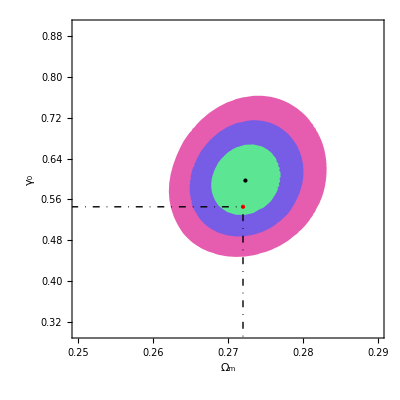

```mathematica
cont=Show[Graphics[Style[{Hue[0.9,.6,.9],Polygon[cont3s[[1,1]]]},Antialiasing->True],Frame->True],Graphics[Style[{Hue[0.7,.6,.9],Polygon[cont2s[[1,1]]]},Antialiasing->True],Frame->True],Graphics[Style[{Hue[0.4,.6,.9],Polygon[cont1s[[1,1]]]},Antialiasing->True],Frame->True],AspectRatio->1,PlotRange->{{0.25,.29},{.3,.9}},FrameLabel->{"Ω_m","γ_0"},Epilog->{{Black,PointSize[Large],Point[{om0,g00}]},{Red,PointSize[Large],Point[{0.272,6/11}]},{DotDashed,Line[{{0,6/11},{0.272,6/11}}],{DotDashed,Line[{{0.272,0},{0.272,6/11}}]}}},TextStyle->{FontFamily->"Times",FontSize->22},PlotRangeClipping->True]
```

```mathematica
output=".\\plots\\contours_LCDM_s8_0.8_G0_om_g0";
Export[output<>".eps",cont,ImageSize->600];
Export[output<>".pdf",cont,ImageSize->600];
(*
Export[deaddrop<>"\\contours_LCDM_s8_0.8_G0_om_g0.eps",cont,ImageSize->600];
Export[deaddrop<>"\\contours_LCDM_s8_0.8_G0_om_g0.pdf",cont,ImageSize->600];
*)
```

```mathematica
(* end *)
```

```mathematica
(* Case 1 *)
```

```mathematica
om0=fmin2[[2,2,1,2]];
g00=fmin2[[2,2,2,2]];
g10=fmin2[[2,2,3,2]];
chi20=chi2R[om0,0,-1,0]+chi2bao[om0,0,-1,0]+chi2SN[om0,0,-1,0];
chi21[g0_,g1_]:=chi20+chi2growth[om0,0,-1,0,g0,g1,σ80,1]
```

```mathematica
(* lim1=FindRoot[{chi21[w0,wa]==fmin1w0wa[[2,1]]+2.30,D[chi21[w0,wa],wa]==0},{{w0,-1.5},{wa,1.5}}] *)
```

```mathematica
fmin2
```

{1659.380318,{573.861,{om→0.272371,g0→0.56666,g1→0.116147}}}

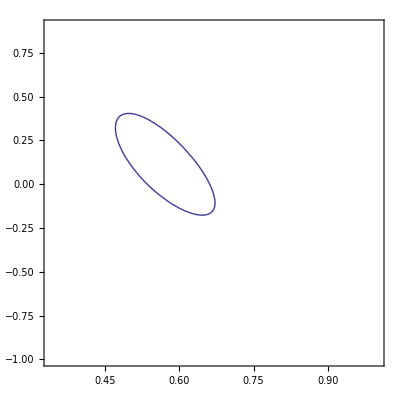
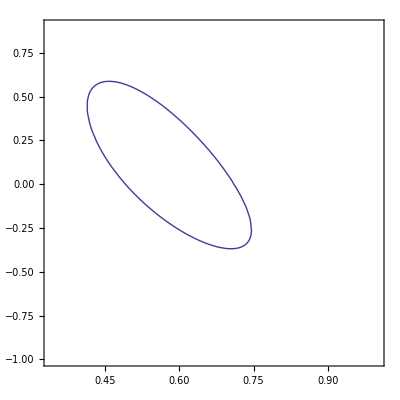
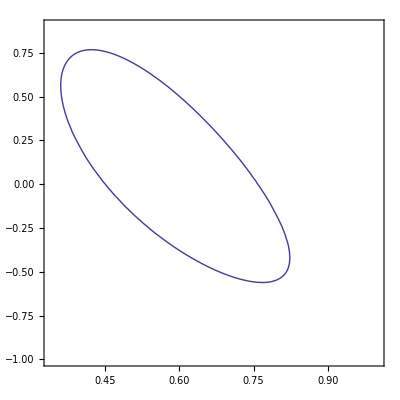

```mathematica
contoursall=Table[ContourPlot[chi21[g0,g1]==fmin2[[2,1]]+dx2[[k]],{g0,0.34,1},{g1,-1,.9},AspectRatio->1,Frame->True,Axes->False],{k,1,3}]
```

```mathematica
Export[".\\backups\\contour_s8_0.8_LCDM_G1_1s.m",contoursall[[1]]]
Export[".\\backups\\contour_s8_0.8_LCDM_G1_2s.m",contoursall[[2]]]
Export[".\\backups\\contour_s8_0.8_LCDM_G1_3s.m",contoursall[[3]]]
```

.\backups\contour_s8_0.8_LCDM_G1_1s.m

.\backups\contour_s8_0.8_LCDM_G1_2s.m

.\backups\contour_s8_0.8_LCDM_G1_3s.m

```mathematica
cont1s=contoursall[[1]];
cont2s=contoursall[[2]];
cont3s=contoursall[[3]];
```

```mathematica
cont1s=Import[".\\backups\\contour_s8_0.8_LCDM_G1_1s.m"];
cont2s=Import[".\\backups\\contour_s8_0.8_LCDM_G1_2s.m"];
cont3s=Import[".\\backups\\contour_s8_0.8_LCDM_G1_3s.m"];
```

```mathematica
g1om=(om^g0+3w0(g0-1/2)(1-om)-3/2 Q0 om^(1-g0)+1/2)/(yp0 Log[om])//FullSimplify;
w0=-1;yp0=1;Q0=1;
```

```mathematica
g1om01=g1om/.g0->6/11/.om->om0
g1om02=g1om/.g0->g00/.om->om0
```

-0.0478231

0.0159141

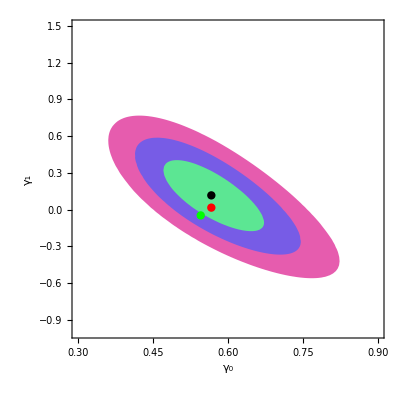

```mathematica
cont=ShowLegend[Show[Graphics[Style[{Hue[0.9,.6,.9],Polygon[cont3s[[1,1]]]},Antialiasing->True],Frame->True],Graphics[Style[{Hue[0.7,.6,.9],Polygon[cont2s[[1,1]]]},Antialiasing->True],Frame->True],Graphics[Style[{Hue[0.4,.6,.9],Polygon[cont1s[[1,1]]]},Antialiasing->True],Frame->True],AspectRatio->1,PlotRange->{{0.3,.9},{-1,1.5}},FrameLabel->{"γ_0","γ_1"},Epilog->{{Black,PointSize[.015],Point[{g00,g10}]},{Green,PointSize[.015],Point[{6/11,g1om01}]},{Red,PointSize[.015],Point[{g00,g1om02}]}},TextStyle->{FontFamily->"Times",FontSize->22},PlotRangeClipping->True],{{{Graphics[{PointSize[.3],Green,Point[{0,0}]}],Style["Σ_1",Large]},{Graphics[{PointSize[.3],Red,Point[{0,0}]}],Style["Σ_2",Large]},
{Graphics[{PointSize[.3],Black,Point[{0,0}]}],Style["BF",Large]}},LegendPosition->{.5,.35},LegendShadow->None,LegendSize->.4}]
```

```mathematica
output=".\\plots\\contours_LCDM_s8_0.8_G1_g0_g1";
Export[output<>".eps",cont,ImageSize->600];
Export[output<>".pdf",cont,ImageSize->600];
(*
Export[deaddrop<>"\\"<>output<>".eps",cont,ImageSize->600];
Export[deaddrop<>"\\"<>output<>".pdf",cont,ImageSize->600];
*)
```

```mathematica
(* end *)
```

```mathematica
(* Case 2 *)
```

```mathematica
om0=fmin3[[2,2,1,2]];
g00=fmin3[[2,2,2,2]];
g10=fmin3[[2,2,3,2]];
chi20=chi2R[om0,0,-1,0]+chi2bao[om0,0,-1,0]+chi2SN[om0,0,-1,0];
chi21[g0_,g1_]:=chi20+chi2growth[om0,0,-1,0,g0,g1,σ80,2]
```

```mathematica
(* lim1=FindRoot[{chi21[w0,wa]==fmin1w0wa[[2,1]]+2.30,D[chi21[w0,wa],wa]==0},{{w0,-1.5},{wa,1.5}}] *)
```

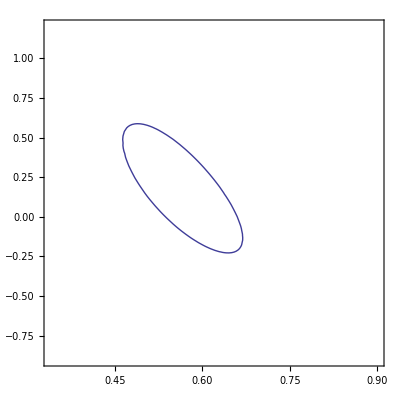
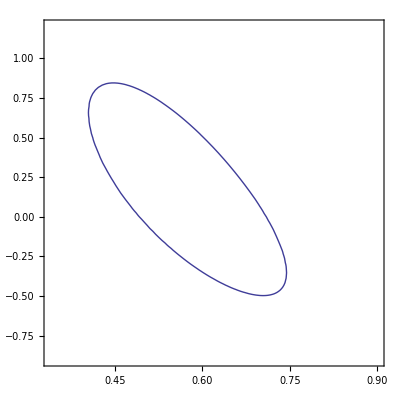
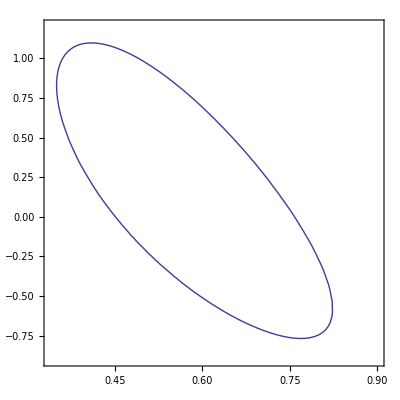

```mathematica
contoursall=Table[ContourPlot[chi21[g0,g1]==fmin3[[2,1]]+dx2[[k]],{g0,0.34,.9},{g1,-.9,1.2},AspectRatio->1,Frame->True,Axes->False],{k,1,3}]
```

```mathematica
Export[".\\backups\\contour_s8_0.8_LCDM_G2_1s.m",contoursall[[1]]]
Export[".\\backups\\contour_s8_0.8_LCDM_G2_2s.m",contoursall[[2]]]
Export[".\\backups\\contour_s8_0.8_LCDM_G2_3s.m",contoursall[[3]]]
```

.\backups\contour_s8_0.8_LCDM_G2_1s.m

.\backups\contour_s8_0.8_LCDM_G2_2s.m

.\backups\contour_s8_0.8_LCDM_G2_3s.m

```mathematica
cont1s=contoursall[[1]];
cont2s=contoursall[[2]];
cont3s=contoursall[[3]];
```

```mathematica
cont1s=Import[".\\backups\\contour_s8_0.8_LCDM_G2_1s.m"];
cont2s=Import[".\\backups\\contour_s8_0.8_LCDM_G2_2s.m"];
cont3s=Import[".\\backups\\contour_s8_0.8_LCDM_G2_3s.m"];
```

```mathematica
g1om=(om^g0+3w0(g0-1/2)(1-om)-3/2 Q0 om^(1-g0)+1/2)/(yp0 Log[om])//FullSimplify;
w0=-1;yp0=1;Q0=1;
```

```mathematica
g1om01=g1om/.g0->6/11/.om->om0
g1om02=g1om/.g0->g00/.om->om0
```

-0.0478246

0.0000248887

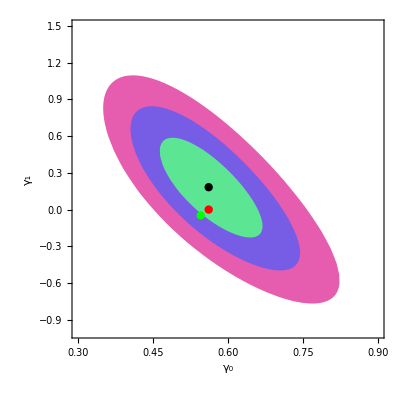

```mathematica
cont=ShowLegend[Show[Graphics[Style[{Hue[0.9,.6,.9],Polygon[cont3s[[1,1]]]},Antialiasing->True],Frame->True],Graphics[Style[{Hue[0.7,.6,.9],Polygon[cont2s[[1,1]]]},Antialiasing->True],Frame->True],Graphics[Style[{Hue[0.4,.6,.9],Polygon[cont1s[[1,1]]]},Antialiasing->True],Frame->True],AspectRatio->1,PlotRange->{{0.3,.9},{-1,1.5}},FrameLabel->{"γ_0","γ_1"},Epilog->{{Black,PointSize[.015],Point[{g00,g10}]},{Green,PointSize[.015],Point[{6/11,g1om01}]},{Red,PointSize[.015],Point[{g00,g1om02}]}},TextStyle->{FontFamily->"Times",FontSize->22},PlotRangeClipping->True],{{{Graphics[{PointSize[.3],Green,Point[{0,0}]}],Style["Σ_1",Large]},{Graphics[{PointSize[.3],Red,Point[{0,0}]}],Style["Σ_2",Large]},
{Graphics[{PointSize[.3],Black,Point[{0,0}]}],Style["BF",Large]}},LegendPosition->{.5,.35},LegendShadow->None,LegendSize->.4}]
```

```mathematica
output=".\\plots\\contours_LCDM_s8_0.8_G2_g0_g1";
Export[output<>".eps",cont,ImageSize->600];
Export[output<>".pdf",cont,ImageSize->600];
(*
Export[deaddrop<>"\\"<>output<>".eps",cont,ImageSize->600];
Export[deaddrop<>"\\"<>output<>".pdf",cont,ImageSize->600];
*)
```

```mathematica
(* end *)
```

```mathematica
(* end *)
```

```mathematica
(* fσ8(z) *)
```

```mathematica
{fσ8z[1,om,0,-1,0,g0,0,σ80,0]/.fmin1[[2,2]],fσ8z[1,om,0,-1,0,g0,g1,σ80,1]/.fmin2[[2,2]],fσ8z[1,om,0,-1,0,g0,g1,σ80,2]/.fmin3[[2,2]],fσ8wCDM[1,-1,0.273,0.8]}
```

{0.424749,0.421993,0.419062,0.424919}

```mathematica
plgr=ErrorListPlot[datagrowth,PlotRange->All,PlotStyle->Gray];
```

```mathematica
pl1=Plot[{fσ8z[z,om,0,-1,0,g0,0,σ80,0]/.fmin1[[2,2]],fσ8z[z,om,0,-1,0,g0,g1,σ80,1]/.fmin2[[2,2]],fσ8z[z,om,0,-1,0,g0,g1,σ80,2]/.fmin3[[2,2]],fσ8wCDM[z,-1,0.273,0.8]},{z,0,0.8},PlotRange->All,PlotStyle->{Blue,Green,Red,Black}];
```

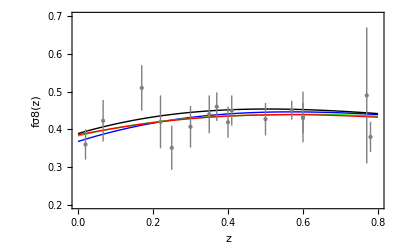

```mathematica
fs8pl=ShowLegend[Show[pl1,plgr,PlotRange->{All,{0.2,.7}},Axes->False,Frame->True,FrameLabel->{"z","fσ8(z)"}],{{{Graphics[{Blue,Line[{{0,0},{1,0}}]}],"Λ+Γ_0"},{Graphics[{Green,Line[{{0,0},{1,0}}]}],"Λ+Γ_1"},
{Graphics[{Red,Line[{{0,0},{1,0}}]}],"Λ+Γ_2"},
{Graphics[{Black,Line[{{0,0},{1,0}}]}],"ΛCDM"}},LegendPosition->{.9,-.3},LegendShadow->None}]
```

```mathematica
Export[".\\plots\\fs8(z)_s8_0.8_LCDM.eps",fs8pl,ImageSize->500]
Export[".\\plots\\fs8(z)_s8_0.8_LCDM.pdf",fs8pl,ImageSize->500]
```

.\plots\fs8(z)_s8_0.8_LCDM.eps

.\plots\fs8(z)_s8_0.8_LCDM.pdf

```mathematica
(* end *)
```

```mathematica
(* γ(z) *)
```

```mathematica
{γ[0][.1,g0,0]/.fmin1[[2,2]],γ[1][.1,g0,g1]/.fmin2[[2,2]],γ[2][.1,g0,g1]/.fmin3[[2,2]],6/11.}
```

{0.596973,0.578275,0.57802,0.545455}

```mathematica
cij1sm=cij1[[2,2]];
cij2sm=cij2[[2;;3,2;;3]];
cij3sm=cij3[[2;;3,2;;3]];
```

```mathematica
sg1[z_]:=(Sum[D[γ[1][z,g0,g1],{g0,g1}[[i]]]D[γ[1][z,g0,g1],{g0,g1}[[j]]] cij2sm[[i,j]],{i,1,2},{j,1,2}])^(1/2)
sg2[z_]:=(Sum[D[γ[2][z,g0,g1],{g0,g1}[[i]]]D[γ[2][z,g0,g1],{g0,g1}[[j]]] cij3sm[[i,j]],{i,1,2},{j,1,2}])^(1/2)
```

```mathematica
pl0=Plot[{γ[0][z,g0,0]+√cij1sm-6/11./.fmin1[[2,2]],γ[0][z,g0,0]-6/11./.fmin1[[2,2]],γ[0][z,g0,0]-√cij1sm-6/11./.fmin1[[2,2]]},{z,0,1},PlotRange->All,PlotStyle->{{Dashed,Blue},Blue,{Dashed,Blue}},BaseStyle->{FontFamily->"Times",FontSize->20}];
pl1=Plot[{(γ[1][z,g0,g1]+sg1[z]-6/11.)/.fmin2[[2,2]],(γ[1][z,g0,g1]-6/11.)/.fmin2[[2,2]],(γ[1][z,g0,g1]-sg1[z]-6/11.)/.fmin2[[2,2]]},{z,0,1},PlotRange->All,PlotStyle->{{Dashed,Green},Green,{Dashed,Green}},BaseStyle->{FontFamily->"Times",FontSize->20}];
pl2=Plot[{γ[2][z,g0,g1]+sg2[z]-6/11./.fmin3[[2,2]],γ[2][z,g0,g1]-6/11./.fmin3[[2,2]],γ[2][z,g0,g1]-sg2[z]-6/11./.fmin3[[2,2]]},{z,0,1},PlotRange->All,PlotStyle->{{Dashed,Red},Red,{Dashed,Red}},BaseStyle->{FontFamily->"Times",FontSize->20}];
```

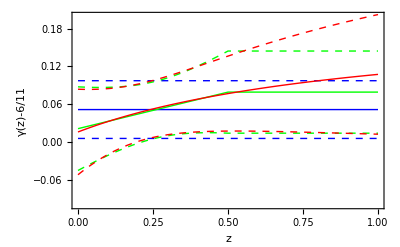

```mathematica
plg1=ShowLegend[Show[pl0,pl1,pl2,PlotRange->{All,{-.1,0.2}},Axes->False,Frame->True,FrameLabel->{"z","γ(z)-6/11"}],{{{Graphics[{Blue,Line[{{0,0},{1,0}}]}],Style["Γ_0",Large]},{Graphics[{Green,Line[{{0,0},{1,0}}]}],Style["Γ_1",Large]},
{Graphics[{Red,Line[{{0,0},{1,0}}]}],Style["Γ_2",Large]}},LegendPosition->{.9,-.1},LegendSize->.4,LegendShadow->None}]
```

```mathematica
Export[".\\plots\\gamma(z)_s8_0.8_LCDM.eps",plg1,ImageSize->500]
Export[".\\plots\\gamma(z)_s8_0.8_LCDM.pdf",plg1,ImageSize->500]
```

.\plots\gamma(z)_s8_0.8_LCDM.eps

.\plots\gamma(z)_s8_0.8_LCDM.pdf

```mathematica
(* end *)
```

```mathematica
(* σ8 free *)
```

```mathematica
(* σ8 free minimization *)
```

```mathematica
(* Γ0 // Om, γ0, γ1=0 *)
fmin1s8=FindMinimum[chi2total[Abs[om],0,-1,0,g0,0,σ8,0],{om,0.27},{g0,6/11},{σ8,0.7}]//AbsoluteTiming
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{762.3448536,{573.254,{om→0.272368,g0→0.523326,σ8→0.761604}}}

```mathematica
(* Γ1 // Om, γ0, γ1 *)
fmin2s8=FindMinimum[chi2total[Abs[om],0,-1,0,g0,g1,σ8,1],{om,0.275},{g0,6/11},{g1,.1},{σ8,0.7}]//AbsoluteTiming
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{2062.354822,{572.618,{om→0.272379,g0→0.48458,g1→-0.398124,σ8→0.693681}}}

```mathematica
(* Γ2 // Om, γ0, γ1 *)
fmin3s8=FindMinimum[chi2total[Abs[om],0,-1,0,g0,g1,σ8,2],{om,0.275},{g0,6/11},{g1,.1},{σ8,0.7}]//AbsoluteTiming
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{3055.190366,{572.652,{om→0.272389,g0→0.48331,g1→-0.633111,σ8→0.684489}}}

```mathematica
(* end *)
```

```mathematica
LaunchKernels[3];
```

```mathematica
(* Γ0 *)
```

```mathematica
Clear[om0,g00,g10,σ8f0,params]
om0=fmin1s8[[2,2,1,2]];
g00=fmin1s8[[2,2,2,2]];
σ8f0=fmin1s8[[2,2,3,2]];
params={om,g0,σ8};
```

```mathematica
case0=ListInterpolation[ParallelTable[chi2total[om,0,-1,0,g0,0,σ8,0],{om,om0-0.01,om0+0.01,0.01},
{g0,g00-0.02,g00+0.02,0.02},{σ8,σ8f0-0.02,σ8f0+0.02,0.02},DistributedContexts->Automatic],{{om0-0.01,om0+0.01},
{g00-0.02,g00+0.02},{σ8f0-0.02,σ8f0+0.02}}]//AbsoluteTiming
```

ListInterpolation::inhr: Requested order is too high; order has been reduced to {2, 2, 2}.

{64.0069124,InterpolatingFunction[{{0.262368,0.282368},{0.503326,0.543326},{0.741604,0.781604}},<>]}

```mathematica
case0[[1]]
```

64.0069124

```mathematica
Export[".\\backups\\chi2_int_LCDM_G0_s8_free.m",case0]
```

.\backups\chi2_int_LCDM_G0_s8_free.m

```mathematica
Fij0=1/2Table[D[case0[[2]][om,g0,σ8],params[[i]],params[[j]]]/.fmin1s8[[2,2]],{i,1,Length[params]},{j,1,Length[params]}]
cij0=Inverse[Fij0]
errors0=√Diagonal[cij0]
```

{{108260.,-870.99,1823.31},{-870.99,493.049,-950.174},{1823.31,-950.174,2530.26}}

{{9.37284×10^-6,0.0000128165,-1.94119×10^-6},{0.0000128165,0.00735775,0.00275378},{-1.94119×10^-6,0.00275378,0.00143073}}

{0.00306151,0.0857773,0.037825}

```mathematica
(* end *)
```

```mathematica
(* Γ1 *)
```

```mathematica
Clear[om0,g00,g10,σ8f0,params]
om0=fmin2s8[[2,2,1,2]];
g00=fmin2s8[[2,2,2,2]];
g10=fmin2s8[[2,2,3,2]];
σ8f0=fmin2s8[[2,2,4,2]];
params={om,g0,g1,σ8};
```

```mathematica
case0=ListInterpolation[ParallelTable[chi2total[om,0,-1,0,g0,g1,σ8,1],{om,om0-0.01,om0+0.01,0.01},
{g0,g00-0.02,g00+0.02,0.02},{g1,g10-0.05,g10+0.05,0.05},{σ8,σ8f0-0.02,σ8f0+0.02,0.02},DistributedContexts->Automatic],{{om0-0.01,om0+0.01},
{g00-0.02,g00+0.02},{g10-0.05,g10+0.05},{σ8f0-0.02,σ8f0+0.02}}]//AbsoluteTiming
```

ListInterpolation::inhr: Requested order is too high; order has been reduced to {2, 2, 2, 2}.

{190.850735,InterpolatingFunction[{{0.262379,0.282379},{0.46458,0.50458},{-0.448124,-0.348124},{0.673681,0.713681}},<>]}

```mathematica
case0[[1]]
```

190.850735

```mathematica
Export[".\\backups\\chi2_int_LCDM_G1_s8_free.m",case0]
```

.\backups\chi2_int_LCDM_G1_s8_free.m

```mathematica
Fij0=1/2Table[D[case0[[2]][om,g0,g1,σ8],params[[i]],params[[j]]]/.fmin2s8[[2,2]],{i,1,Length[params]},{j,1,Length[params]}]
cij0=Inverse[Fij0]
errors0=√Diagonal[cij0]
```

{{107412.,-584.668,-134.809,1190.02},{-584.668,461.812,117.294,-999.513},{-134.809,117.294,56.2267,-395.03},{1190.02,-999.513,-395.03,3051.31}}

{{9.37519×10^-6,0.0000132316,-3.99923×10^-6,1.60156×10^-7},{0.0000132316,0.00948933,0.0225384,0.00602111},{-3.99923×10^-6,0.0225384,0.250313,0.0397905},{1.60156×10^-7,0.00602111,0.0397905,0.00745135}}

{0.00306189,0.0974132,0.500313,0.0863212}

```mathematica
(* end *)
```

```mathematica
(* Γ2 *)
```

```mathematica
Clear[om0,g00,g10,σ8f0,params]
om0=fmin3s8[[2,2,1,2]];
g00=fmin3s8[[2,2,2,2]];
g10=fmin3s8[[2,2,3,2]];
σ8f0=fmin3s8[[2,2,4,2]];
params={om,g0,g1,σ8};
```

```mathematica
case0=ListInterpolation[ParallelTable[chi2total[om,0,-1,0,g0,g1,σ8,2],{om,om0-0.01,om0+0.01,0.01},
{g0,g00-0.02,g00+0.02,0.02},{g1,g10-0.05,g10+0.05,0.05},{σ8,σ8f0-0.02,σ8f0+0.02,0.02},DistributedContexts->Automatic],{{om0-0.01,om0+0.01},
{g00-0.02,g00+0.02},{g10-0.05,g10+0.05},{σ8f0-0.02,σ8f0+0.02}}]//AbsoluteTiming
```

ListInterpolation::inhr: Requested order is too high; order has been reduced to {2, 2, 2, 2}.

{190.196341,InterpolatingFunction[{{0.262389,0.282389},{0.46331,0.50331},{-0.683111,-0.583111},{0.664489,0.704489}},<>]}

```mathematica
case0[[1]]
```

190.196341

```mathematica
Export[".\\backups\\chi2_int_LCDM_G2_s8_free.m",case0]
```

.\backups\chi2_int_LCDM_G2_s8_free.m

```mathematica
Fij0=1/2Table[D[case0[[2]][om,g0,g1,σ8],params[[i]],params[[j]]]/.fmin3s8[[2,2]],{i,1,Length[params]},{j,1,Length[params]}]
cij0=Inverse[Fij0]
errors0=√Diagonal[cij0]
```

{{107317.,-547.18,-89.8398,1086.13},{-547.18,457.653,86.4448,-1004.4},{-89.8398,86.4448,29.407,-293.404},{1086.13,-1004.4,-293.404,3133.73}}

{{9.37662×10^-6,0.0000135035,-4.43223×10^-6,6.63169×10^-7},{0.0000135035,0.0094578,0.037009,0.00649171},{-4.43223×10^-6,0.037009,0.661595,0.0738068},{6.63169×10^-7,0.00649171,0.0738068,0.00930988}}

{0.00306213,0.0972512,0.813385,0.0964877}

```mathematica
(* end *)
```

```mathematica
(* end *)
```